```mathematica
F[x_]:=1/2 ⅈ (PolyLog[2,-ⅈ ⅇ^x]-PolyLog[2,ⅈ ⅇ^x])
```

```mathematica
G3[a_,b_]:=F[a-b]+F[b-a]-π/2(a+b);
```

```mathematica
EnergySetup[n_,FacesCW_]:=Module[{i,rhoV,rhoF,include,LineFaces,f,Faces,NM,nonlinefaces,radii,RADII},
Faces=Sort/@FacesCW;
f=Length[Faces];
LineFaces={};rhoV=Table[Subscript[rV, i],{i,1,n-2}];rhoF=Table[Subscript[rF, i],{i,1,f-2}];
include = {};
nonlinefaces={};
For[i=1,i≤f,i++,
If[!(Faces[[i,-2]]==n-1&&Faces[[i,-1]]==n),
(* then *) AppendTo[include,i];AppendTo[nonlinefaces,FacesCW[[i]]],
(* else *) AppendTo[LineFaces,i]]];

NM=NMinimize[{∑_(k=1)^(f-2) ∑_(i=1)^Length[Faces[[include[[k]]]]] If[Faces[[include[[k]],i]]<n-1,G3[Subscript[rV, Faces[[include[[k]],i]]],Subscript[rF, k]],0]+∑_(i=1)^(n-2) Subscript[rV, i] π If[MemberQ[Flatten@Table[Faces[[LineFaces[[m]]]],{m,1,2}],i],(* then *) 1,(* else *) 2]+∑_(j=1)^(f-2) Subscript[rF, j] π If[MemberQ[Faces[[include[[j]]]],n-1]||MemberQ[Faces[[include[[j]]]],n],(* then *) 1,(* else *) 2],
∑_(i=1)^(n-2) Subscript[rV, i]+∑_(j=1)^(f-2) Subscript[rF, j]==0},Join[rhoV,rhoF]];
RADII=Exp[Re[Join[rhoV,rhoF]/.(NM[[2]])]];
RADII/=RADII[[1]];
radii=<||>;
For[i=1,i≤n-2,i++,
radii[i]=RADII[[i]]
];
For[i=1,i≤Length[nonlinefaces],i++,
radii[nonlinefaces[[i]]]=RADII[[n-2+i]]
];
{radii,LineFaces}
];
```

```mathematica
Boundary[n_,FacesCW_,LineFaces_,radii_,ϵ_:0]:=Module[{i,j,faces,vertices,lastvisited,d,h,H,breaker,unvisited,f,endcircle,ComputeEndcircle,ComputeEndcircle2,delete},
unvisited =FacesCW;(*Keeps track of the faces we haven't visited*)
f=Length[FacesCW];

faces=<||>; (* centers of face circles (or normals, for lines) *)
For[i=1,i≤f,i++,faces[FacesCW[[i]]]={-∞,-∞}];
vertices=<||>; (* centers of vertex circles (or normals, for lines) *)
For[i=1,i≤n-2,i++,vertices[i]={-∞,-∞}];
(* Radii is an assoc from v->rad and facelist->rad *)

(*Vertex circles going vertically upwards along first FaceLine*)
h=0; (* height along the left line *)
For[i=1,i≤Length[FacesCW[[LineFaces[[1]]]]]-2(*Number of vertex circles that lie along first LineFace*),i++,
vertices[FacesCW[[LineFaces[[1]],i]]]={0,h+radii[FacesCW[[LineFaces[[1]],i]]]};(*Set the center of this vertex circle*)
h+=2radii[[FacesCW[[LineFaces[[1]],i]]]]];(*Keeps track of our cumulative height as we climb up the first FaceLine*)

unvisited=Delete[unvisited,Position[unvisited,FacesCW[[LineFaces[[1]]]]]];

d=0;(*Horizontal distance*)

ComputeEndcircle[prev_,face_]:=
(*Returns which vertex circle we calculated last based on previous vertex circle and face*)
If[face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n-1][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle[n,FacesCW[[LineFaces[[1]]]]];(*Previous vertex circle is bottom line, face is first FaceLine*)

(*Face circles going horizontally across upper vertex line*)
breaker=True;
For[j=1,j≤f ,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n-1], (*determine if this face-circle contains n-1, so it is on the upper vertex line*)
If[MemberQ[unvisited[[i]],ComputeEndcircle[endcircle,unvisited[[i]]]],
(*determine if this face-circle also contains the vertex right before n-1 to ensure we are going horizontally across in the right order*)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing--find the other face circle containing endcircle*)
,
(* else if the face circle is not a line*)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (*Set the center of this face circle*)
d+=2radii[unvisited[[i]]]; (* update how far along the top line we are *)
endcircle=ComputeEndcircle[endcircle,unvisited[[i]]];(*Update endcircle*)
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Vertex circles along the second FaceLine, climbing vertically upwards*)
h=0;
For[i=1,i≤Length[FacesCW[[LineFaces[[2]]]]]-2,i++,
vertices[FacesCW[[LineFaces[[2]],i]]]={d,h+radii[FacesCW[[LineFaces[[2]],i]]]};h+=2radii[[FacesCW[[LineFaces[[2]],i]]]]];
H=h;
h=0;(*Reset height*)

ComputeEndcircle2[prev_,face_]:=
If[face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle2[n-1,FacesCW[[LineFaces[[1]]]]];
(*Face circles along lower vertex line, moving horizontally from origin to second FaceLine*)
d=0;(*Reset distance*)
breaker=True;
For[j=1,j≤f,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n], (* determine if this face-circle contains n *)
If[MemberQ[unvisited[[i]],endcircle(* ComputeEndcircle2[endcircle,unvisited[[i]]] *)],(* determine if this face-cirlce also contains the vertex right before n *)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing*)
,
(* else *)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (* then we'll make this face's center be where we know it is *)
d+=2radii[unvisited[[i]]]; (* update how far along the bottom line we are *)
endcircle=ComputeEndcircle2[endcircle,unvisited[[i]]];
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Set the normals of the vertex lines and face lines*)
faces[FacesCW[[LineFaces[[2]]]]]={1,0};
faces[FacesCW[[LineFaces[[1]]]]]={-1,0};
vertices[n]={0,-1};
vertices[n-1]={0,1};

If[ThrowOrderError[faces,vertices,radii,d,H,n,FacesCW[[LineFaces]],0],
faces[FacesCW[[LineFaces[[1]]]]]*=-1;
faces[FacesCW[[LineFaces[[2]]]]]*=-1;
For[i=1,i≤n,i++,
If[i==n-1||i==n,
,
If[Abs[vertices[i][[1]]-d]≤ϵ,
vertices[i]={0,vertices[i][[2]]},
If[Abs[vertices[i][[1]]-0]≤ϵ,
vertices[i]={d,vertices[i][[2]]}]];
]]];

(*Return the assoc's of the faces to their centers and vertices to their centers*)
{vertices,faces,d,H}
];
```

```mathematica
FindRest[{x_,y_},r_,face_,vertices_,radii_,lines_]:=(* face is all the vertices that the face intersects *)
(*{x_,y_},r: known center of opposite kind and its radius
face: all the circles of its kind that pass thru that opposite known circle
vertices: all the circles of its kind that are tangent to the one we'e looking for*)
Module[{verts=vertices,i,j,ϕ,θ,ω,face2=face,b,b2=True},

If[verts[face2[[1]]]=={-∞,-∞}||MemberQ[lines,face2[[1]]],
For[i=2,i≤Length[face2]&&b2,i++,
If[verts[face2[[i]]]≠{-∞,-∞}&&!MemberQ[lines,face2[[i]]],
face2=Join[face2[[i;;]],face2[[;;i-1]]];
b2=False;
]]];

b=True;
For[i=2,i≤Length[face2]&&b,i++,
If[MemberQ[lines,face2[[i]]],
AppendTo[face2,face2[[1]]];
For[j=Length[face2]-1,j>i,j--,
If[verts[face2[[j]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[j+1]]][[1]]-x,verts[face2[[j+1]]][[2]]-y];
θ=ArcTan[radii[face2[[j+1]]]/r];(* j+1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[j]]]/r];
verts[face2[[j]]]={x+√(r^2+radii[face2[[j]]]^2)Cos[ϕ-θ-ω],y+√(r^2+radii[face2[[j]]]^2)Sin[ϕ-θ-ω]}
]
];b=False;Break,
If[verts[face2[[i]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[i-1]]][[1]]-x,verts[face2[[i-1]]][[2]]-y];
θ=ArcTan[radii[face2[[i-1]]]/r];(* i-1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[i]]]/r];
verts[face2[[i]]]={x+√(r^2+radii[face2[[i]]]^2)Cos[ϕ+θ+ω],y+√(r^2+radii[face2[[i]]]^2)Sin[ϕ+θ+ω]}];
];];
verts
];
```

```mathematica
Cull[assoc_]:=Module[{vis={},unv={},i},For[i=1,i≤Length[Keys[assoc]],i++,If[assoc[Keys[assoc][[i]]]=={-∞,-∞},AppendTo[unv,Keys[assoc][[i]]],AppendTo[vis,Keys[assoc][[i]]]]];{vis,unv}]
```

```mathematica
Interior[n_,FacesCW_,LineFaces_,radii_,vertices_,faces_,d_,h_]:=
Module[{Vunv={},Funv={},Vvis={},Fvis={},i,j,f,verts=vertices,verts2,fcs=faces,fcs2,fi,vi,x,y,k,b},
f=Length[FacesCW];
For[i=1,i≤n,i++,
If[vertices[i]=={-∞,-∞},AppendTo[Vunv,i],AppendTo[Vvis,i]]];
For[i=1,i≤f,i++,
If[faces[FacesCW[[i]]]=={-∞,-∞},AppendTo[Funv,FacesCW[[i]]],AppendTo[Fvis,FacesCW[[i]]]]];

For[j=1,j≤n+Length[FacesCW]&&(Length[Vunv]+Length[Funv]>0),j++,

For[i=1,i≤Length[Fvis],i++,(* for a known face circle *)
If[Length[Intersection[Vvis,Fvis[[i]]]]*Length[Intersection[Vunv,Fvis[[i]]]]>0,
fi=Fvis[[i]];
{x,y}=fcs[fi];
verts2=FindRest[{x,y},radii[fi],fi,verts,radii,{n-1,n}];
If[ThrowOrderError[fcs,verts2,radii,d,h,n,{FacesCW[[LineFaces[[1]]]],FacesCW[[LineFaces[[2]]]]},0],verts=FindRest[{x,y},radii[fi],Reverse[fi],verts,radii,{n-1,n}],
verts=verts2];
];
{Vvis,Vunv}=Cull[verts];
];

For[i=1,i≤Length[Vvis],i++, (* for a known vertex circle *)
If[b=False;
For[k=1,k≤Length[Fvis],k++,b=b||If[MemberQ[Fvis[[k]],Vvis[[i]]],True,False]];b,
If[b=False;For[k=1,k≤Length[Funv],k++,b=b||If[MemberQ[Funv[[k]],Vvis[[i]]],True,False]];b,
(* then *)
vi=Vvis[[i]];
{x,y}=verts[vi];
fcs2=FindRest[{x,y},radii[vi],FacesList[vi,FacesCW],fcs,radii,FacesCW[[LineFaces]]];
If[ThrowOrderError[fcs2,verts,radii,d,h,n,FacesCW[[LineFaces]],0],
fcs=FindRest[{x,y},radii[vi],
Reverse[FacesList[vi,FacesCW]],fcs,radii,FacesCW[[LineFaces]]],
fcs=fcs2];
];
{Fvis,Funv}=Cull[fcs];
]
];
];
{verts,fcs}
];
```

```mathematica
ThrowOrderError[fcs2_,verts_,radii_,d_,h_,n_,fls_,ϵ_](* fcs2 is proposed fcs association. fls is facelines *):=
Module[{i,j,b,b2,K},
K={};
For[i=1,i≤Length[Keys[fcs2]],i++,
If[!MemberQ[fls,Keys[fcs2][[i]]],AppendTo[K,Keys[fcs2][[i]]]]
];

b=False; (* "breaker" *)
For[i=1,i≤Length[K]&&!b,i++,
If[b2=False;
-∞<fcs2[K[[i]]][[1]]<0
||-∞<fcs2[K[[i]]][[2]]<0
||fcs2[K[[i]]][[1]]>d
||fcs2[K[[i]]][[2]]>h
||(For[j=1,j≤Length[K[[i]]],j++,
If[K[[i,j]]≠n-1&&K[[i,j]]≠n&&verts[K[[i,j]]]≠{-∞,-∞}&&fcs2[K[[i]]]≠{-∞,-∞},
If[EuclideanDistance[verts[K[[i,j]]],fcs2[K[[i]]]]≥(1-ϵ)(radii[K[[i,j]]]+radii[K[[i]]]),b2=True;Break]]];b2),
b=True,

For[j=1,j≤Length[K]&&!b,j++,
If[i≠j&&fcs2[K[[i]]]≠{-∞,-∞}&&fcs2[K[[j]]]≠{-∞,-∞}&&
EuclideanDistance[fcs2[K[[i]]],fcs2[K[[j]]]]<(1+ϵ)(radii[fcs2[K[[i]]]]+radii[fcs2[K[[j]]]])
,(* then, bad *) b=True]]];
];


For[i=1,i≤Length[fls[[1]]]&&!b,i++,
If[verts[fls[[1,i]]][[1]]≠d/2+fcs2[fls[[1]]][[1]] d/2&&fls[[1,i]]<n-1,b=True]
];
For[i=1,i≤Length[fls[[2]]]&&!b,i++,
If[verts[fls[[2,i]]][[1]]≠d/2+fcs2[fls[[2]]][[1]] d/2&&fls[[2,i]]<n-1,b=True]
];

b
];
```

```mathematica
FacesList[v_,Faces_]:=
Module[{ContainV={},i,L=2,p=3,temp},
For[i=1,i≤Length[Faces],i++,
If[MemberQ[Faces[[i]],v],AppendTo[ContainV,Faces[[i]]]]];
While[L<Length[ContainV],
While[p≤Length[ContainV],
If[Length[Intersection[ContainV[[L-1]],ContainV[[p]]]]==2,
temp=ContainV[[p]];ContainV[[p]]=ContainV[[L]];ContainV[[L]]=temp;p=1+Length[ContainV],
p++]
];
L++;
p=L+1;
];
ContainV];
```

```mathematica
Q=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
InvCoords[z_,r_,d_:0]:=If[r==∞,{2d,0,z},{Norm[z]^2/r-r,1/r,z/r}];
```

```mathematica
Gram[SC_]:=SC.Q.Transpose[SC];
SuperCluster[vertices_,faces_,radii_,fls_,d_,h_,n_]:=
Module[{sc={},i},
For[i=1,i≤n-2,i++,AppendTo[sc,Flatten[InvCoords[vertices[i],radii[i]]]]];
AppendTo[sc,Flatten[InvCoords[vertices[n-1],∞,h/2+vertices[n-1][[2]] h/2]]];
AppendTo[sc,Flatten[InvCoords[vertices[n],∞,h/2+vertices[n][[2]] h/2]]];
For[i=1,i≤Length[Keys[faces]],i++,
If[!MemberQ[fls,Keys[faces][[i]]],
AppendTo[sc,Flatten[InvCoords[faces[Keys[faces][[i]]],radii[Keys[faces][[i]]]]]]
]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[1]]],∞,d/2+faces[fls[[1]]][[1]] d/2]]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[2]]],∞,d/2+faces[fls[[2]]][[1]] d/2]]];
sc
];
```

```mathematica
DrawCircle[{bhat_,b_,bx_,by_}]:=If[Abs[b]≥ .01,Circle[{bx,by}/b,1/b],InfiniteLine[{bx,by}bhat/2,{-by,bx}]];
```

```mathematica
Packing[n_,FacesCW_,ϵ_:0]:=
Module[{radii,LineFaces,vertices,faces,d,h},
{radii,LineFaces}=EnergySetup[n,FacesCW];
{vertices,faces,d,h}=Boundary[n,FacesCW,LineFaces,radii,ϵ];
{vertices,faces}=Interior[n,FacesCW,LineFaces,radii,vertices,faces,d,h];
{vertices,faces,radii,d,h,LineFaces}];
```

```mathematica
Render[radii_,fcs_,verts_,fls_,n_,d_,h_]:=Graphics[{Blue,Thick,
Table[If[i==n-1,Line[{{-Max[Values[radii]],h},{d+Max[Values[radii]],h}}],If[i==n,Line[{{-Max[Values[radii]],0},{d+Max[Values[radii]],0}}],
Circle[verts[Keys[verts][[i]]],radii[Keys[verts][[i]]]]]],{i,1,n}],
Red,Dashed,
Table[If[Keys[fcs][[i]]==fls[[1]],Line[{{0,-Max[Values[radii]]},{0,h+Max[Values[radii]]}}],
If[Keys[fcs][[i]]==fls[[2]],Line[{{d,-Max[Values[radii]]},{d,h+Max[Values[radii]]}}],
Circle[fcs[Keys[fcs][[i]]],radii[Keys[fcs][[i]]]]]],{i,1,Length[Keys[fcs]]}]
}];
```

```mathematica
SendToInt[ϵ_:0][y_]:=With[{x=Simplify[y]},If[Abs[x-Floor[x]]≤ϵ ,Floor[x],
If[Abs[x-Ceiling[x]]≤ ϵ ,Ceiling[x],x],x]];
```

```mathematica
R[vhat_]:=IdentityMatrix[4]+2Q.Transpose[{vhat}].{vhat}
BMat[n_]:=Table[b[i,j],{i,1,n},{j,1,n}];

Bend[V_,m_][i_]:=
Module[{sol,assignments,rest,l,others1,others2},
sol=Solve[BMat[m].(V[[;;m]])==(V[[;;m]]).R[V[[m+i]]]][[1]];
assignments=Association[sol];
rest=Complement[Flatten[BMat[m]],Keys[assignments]];
l=Length[rest];
others1=Solve[rest==Table[0,{j,1,l}]][[1]];
others2=<||>;
For[j=1,j≤l,j++,others2[rest[[j]]]=Subscript[a, j]];
others2=Normal[others2];
Column[{
MatrixForm[(BMat[m]/.assignments)/.others2],
MatrixForm[(BMat[m]/.assignments)/.others1]
}]
];
```

```mathematica
Everything[n_,FacesCW_,ϵ_:0,steps_,sizemax_:∞]:=Module[{vertices,faces,f=Length[FacesCW],radii,d,h,LineFaces,Vnye,Vout,bends={}},
{vertices,faces,radii,d,h,LineFaces}=Packing[n,FacesCW,ϵ];
Vnye=SendToInt[ϵ]//@SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n];
Vout=MatrixForm[Simplify[RootApproximant[Vnye]]];
bends=Bend[Vout[[1]],n]/@Range@f;
Column[{
Render[radii,faces,vertices,FacesCW[[LineFaces]],n,d,h],
Graphics[{Thick, DrawCircle/@Orbit[Vnye[[-f;;]],Vnye[[;;n]],steps,sizemax],Red,DrawCircle/@Vnye[[-f;;]], Blue, DrawCircle/@Vnye[[;;n]]},PlotRange->{{-d,2 d},{-1.2 Max[Values[radii]],h+1.2 Max[Values[radii]]}},PlotRangeClipping->True],
Vout,
bends,
MatrixForm[Simplify[RootApproximant[
SendToInt[ϵ]//@Gram[SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n]]]
]]
}]]
```

```mathematica
Orbit[co_,cl_,steps_,sizemax_:∞]:=Module[{i,j,k,orbit=cl,L},
For[i=1,i≤steps,i++,
L=Length[orbit];
For[j=1,j≤Length[co],j++,
For[k=1,k≤L,k++,
If[(orbit⟦k⟧.R[co⟦j⟧])⟦2⟧≤sizemax&&!MemberQ[Round[N[orbit],.001],Round[N[orbit⟦k⟧.R[co⟦j⟧]],.001](*new thing*)],AppendTo[orbit,orbit⟦k⟧.R[co⟦j⟧](*newthing*)]]
]
]
];
orbit
];
```

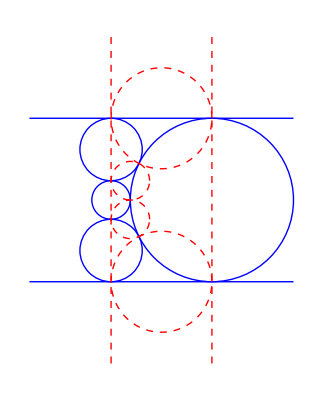
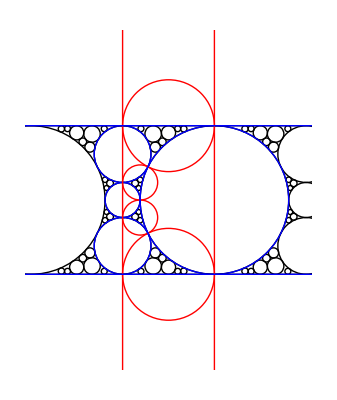
-Graphics-
-Graphics-
(Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1] | 1 | 8362/6765 | 1
0 | 9959/3804 | 0 | 1
4 | 10641/2512 | 0 | 6765/1597
Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] | 9349/3571 | 0 | 30559/7214
229826875+√52820391694962013 | 57456708+√(6602546745531133/2) | 0 | 1/6 (689480561+√475383444777364069)
4 | 0 | 0 | 1
0 | 0 | 0 | -1
16491/2548 | 13907/8595 | 1 | 11323/3499
0 | 6765/4181 | 1 | 0
Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3] | 22879/5401 | 1 | 11323/3499
18931/2925 | 15127/3571 | 1 | 11933/2279
15127/6119 | 0 | 1 | 0
0 | 0 | -1 | 0)
{((-42717724638207+55918223124764 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/42717728514552 | (18432015403 (-85435453152759+55918223124764 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/2061371748250652925537450-(10119591 a_1)/6254252-(35563596 a_2)/35563589-(1902 (114913416+√13205093491062266) a_3)/9959 | a_1 | a_2 | a_3 | (-1963559346085374528363+1530611067891823395478 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-160645785668440752680 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/490889922870404016960-a_1-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_2-1/4 (229826875+√52820391694962013) a_3 | (181732171222975393066228921521723-45432995380502971375256444680358 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-48114379878459921945804854568600 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/147024487005478241010309677419200+(16160987509 a_1)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_2)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_3)/119508
800876485043745/94530680203232 | 9010660786168469387/2127129291382116840-(10119591 a_4)/6254252-(35563596 a_5)/35563589-(1902 (114913416+√13205093491062266) a_6)/9959 | a_4 | a_5 | a_6 | -(355155869199 (-22982957+2872870 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/481728346315670272-a_4-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_5-1/4 (229826875+√52820391694962013) a_6 | -(118385289733 (2127128311686219997+860441859375748650 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/48093513225202196811964020480+(16160987509 a_4)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_5)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_6)/119508
24251348255919385337/4631599287664911744 | 77955569518097613532207807/21546402518686004772976800-(10119591 a_7)/6254252-(35563596 a_8)/35563589-(1902 (114913416+√13205093491062266) a_9)/9959 | a_7 | a_8 | a_9 | -(11 (-123078335968561944905189+14043735308200589508790 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/118013149849701951237120-a_7-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_8-1/4 (229826875+√52820391694962013) a_9 | (-7459618739761243593018146373730993-2011652866643410299946706356136850 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/1536767339424193429001964460108800+(16160987509 a_7)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_8)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_9)/119508
(451 (-10336192522590747555+1597029039969325508 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/550229845751352947544 | (317 (-415280447798040831491942445+92859507456633786785415772 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/58872946244794047274321290150-(10119591 a_10)/6254252-(35563596 a_11)/35563589-(1902 (114913416+√13205093491062266) a_12)/9959 | a_10 | a_11 | a_12 | (-56818050296681339309835+9617176242717629214356 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/3353230440024987587520-(451 (-10336192522590747555+1597029039969325508 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/2200919383005411790176-a_10-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_11-1/4 (229826875+√52820391694962013) a_12 | (7267273377171943145532279327269235-1373933211332691540570662847092596 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/1004312702882643536684893173710400-(451 (-10336192522590747555+1597029039969325508 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/21918956135350896018362784+(16160987509 a_10)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_11)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_12)/119508
(451 (1490621561560+495948767355 √13205093491062266+247974381928 √52820391694962013-165316252920 √475383444777364069))/85435457029104 | (317 (632872297514818230354793640+34344403082449101045 √13205093491062266+14418509865130286552 √52820391694962013-9612339811317614280 √475383444777364069))/9141338129714647119900-(10119591 a_13)/6254252-(35563596 a_14)/35563589-(1902 (114913416+√13205093491062266) a_15)/9959 | a_13 | a_14 | a_15 | (29915643051004118795320+2726230374150435 √13205093491062266+1493281133276296 √52820391694962013-908743442301240 √475383444777364069)/520663823272320-(451 (1490621561560+495948767355 √13205093491062266+247974381928 √52820391694962013-165316252920 √475383444777364069) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/341741828116416-a_13-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_14-1/4 (229826875+√52820391694962013) a_15 | (-5537530651821816693286056089796920-474856268470406952604179435 √13205093491062266-213333778136633191857592136 √52820391694962013+142222517029325603635859640 √475383444777364069)/155941949411606237922806400-(451 (1490621561560+495948767355 √13205093491062266+247974381928 √52820391694962013-165316252920 √475383444777364069) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/3403406866211386944+(16160987509 a_13)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_14)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_15)/119508
451/8382599787 | 73728061612/3587652327203550675-(10119591 a_16)/6254252-(35563596 a_17)/35563589-(1902 (114913416+√13205093491062266) a_18)/9959 | a_16 | a_17 | a_18 | (213588665555717-2872870 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/213588642572760-a_16-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_17-1/4 (229826875+√52820391694962013) a_18 | (-2127128311686219997-860441859375748650 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/63971084231743100545060200+(16160987509 a_16)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_17)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_18)/119508
76600095/14629319 | 834822841632676/417411556393665-(10119591 a_19)/6254252-(35563596 a_20)/35563589-(1902 (114913416+√13205093491062266) a_21)/9959 | a_19 | a_20 | a_21 | -(2613 (-22982957+2872870 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/5734693048-a_19-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_20-1/4 (229826875+√52820391694962013) a_21 | (-1280203729436695554067-749444859516277074150 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/572525030042002063320+(16160987509 a_19)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_20)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_21)/119508)
((-42717724638207+55918223124764 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/42717728514552 | (18432015403 (-85435453152759+55918223124764 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/2061371748250652925537450 | 0 | 0 | 0 | (-1963559346085374528363+1530611067891823395478 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-160645785668440752680 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/490889922870404016960 | (181732171222975393066228921521723-45432995380502971375256444680358 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-48114379878459921945804854568600 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/147024487005478241010309677419200
800876485043745/94530680203232 | 9010660786168469387/2127129291382116840 | 0 | 0 | 0 | -(355155869199 (-22982957+2872870 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/481728346315670272 | -(118385289733 (2127128311686219997+860441859375748650 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/48093513225202196811964020480
24251348255919385337/4631599287664911744 | 77955569518097613532207807/21546402518686004772976800 | 0 | 0 | 0 | -(11 (-123078335968561944905189+14043735308200589508790 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/118013149849701951237120 | (-7459618739761243593018146373730993-2011652866643410299946706356136850 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/1536767339424193429001964460108800
(451 (-10336192522590747555+1597029039969325508 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/550229845751352947544 | (317 (-415280447798040831491942445+92859507456633786785415772 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/58872946244794047274321290150 | 0 | 0 | 0 | (-56818050296681339309835+9617176242717629214356 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/3353230440024987587520-(451 (-10336192522590747555+1597029039969325508 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/2200919383005411790176 | (7267273377171943145532279327269235-1373933211332691540570662847092596 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/1004312702882643536684893173710400-(451 (-10336192522590747555+1597029039969325508 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/21918956135350896018362784
(451 (1490621561560+495948767355 √13205093491062266+247974381928 √52820391694962013-165316252920 √475383444777364069))/85435457029104 | (317 (632872297514818230354793640+34344403082449101045 √13205093491062266+14418509865130286552 √52820391694962013-9612339811317614280 √475383444777364069))/9141338129714647119900 | 0 | 0 | 0 | (29915643051004118795320+2726230374150435 √13205093491062266+1493281133276296 √52820391694962013-908743442301240 √475383444777364069)/520663823272320-(451 (1490621561560+495948767355 √13205093491062266+247974381928 √52820391694962013-165316252920 √475383444777364069) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/341741828116416 | (-5537530651821816693286056089796920-474856268470406952604179435 √13205093491062266-213333778136633191857592136 √52820391694962013+142222517029325603635859640 √475383444777364069)/155941949411606237922806400-(451 (1490621561560+495948767355 √13205093491062266+247974381928 √52820391694962013-165316252920 √475383444777364069) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/3403406866211386944
451/8382599787 | 73728061612/3587652327203550675 | 0 | 0 | 0 | (213588665555717-2872870 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/213588642572760 | (-2127128311686219997-860441859375748650 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/63971084231743100545060200
76600095/14629319 | 834822841632676/417411556393665 | 0 | 0 | 0 | -(2613 (-22982957+2872870 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/5734693048 | (-1280203729436695554067-749444859516277074150 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/572525030042002063320),((-34961522+45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/34961522 | (1902 (-69923044+45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/174090898799-(10119591 a_1)/6254252-(35563596 a_2)/35563589-(1902 (114913416+√13205093491062266) a_3)/9959 | a_1 | a_2 | a_3 | (69923044 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/139846088-a_1-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_2-1/4 (229826875+√52820391694962013) a_3 | (-3849403418288+3215830761896 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-455775875775 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/1392727190392+(16160987509 a_1)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_2)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_3)/119508
0 | 1-(10119591 a_4)/6254252-(35563596 a_5)/35563589-(1902 (114913416+√13205093491062266) a_6)/9959 | a_4 | a_5 | a_6 | -a_4-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_5-1/4 (229826875+√52820391694962013) a_6 | (16160987509 a_4)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_5)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_6)/119508
91530450/17480761 | 395556342059151/109329084445772-(10119591 a_7)/6254252-(35563596 a_8)/35563589-(1902 (114913416+√13205093491062266) a_9)/9959 | a_7 | a_8 | a_9 | (34961522-45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/34961522-a_7-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_8-1/4 (229826875+√52820391694962013) a_9 | (980900606310234251-228552459114379950 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/174598547859897884+(16160987509 a_7)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_8)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_9)/119508
(45765225 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/34961522 | (1902 (326855269178+163427618475 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/621678599611229-(10119591 a_10)/6254252-(35563596 a_11)/35563589-(1902 (114913416+√13205093491062266) a_12)/9959 | a_10 | a_11 | a_12 | (34961522 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-45765225 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/139846088-a_10-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_11-1/4 (229826875+√52820391694962013) a_12 | (-58052344100722688108+36937030646589925906 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-5870665378179837675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/17939157670381624024+(16160987509 a_10)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_11)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_12)/119508
(45765225 (229826875+√52820391694962013))/34961522 | (1902 (12526852606211451+17480761 √13205093491062266+45765225 √52820391694962013))/174090898799-(10119591 a_13)/6254252-(35563596 a_14)/35563589-(1902 (114913416+√13205093491062266) a_15)/9959 | a_13 | a_14 | a_15 | -((229826875+√52820391694962013) (-34961522+45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/139846088-a_13-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_14-1/4 (229826875+√52820391694962013) a_15 | (405945231460167809521+398980889064 √13205093491062266+2611363687197 √52820391694962013-348181797598 √475383444777364069)/2089090785588-(45765225 (229826875+√52820391694962013) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1392727190392+(16160987509 a_13)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_14)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_15)/119508
91530450/17480761 | 348181831800/174090898799-(10119591 a_16)/6254252-(35563596 a_17)/35563589-(1902 (114913416+√13205093491062266) a_18)/9959 | a_16 | a_17 | a_18 | (34961522-45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/34961522-a_16-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_17-1/4 (229826875+√52820391694962013) a_18 | -(45765225 (-55052+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/348181797598+(16160987509 a_16)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_17)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_18)/119508
0 | -(10119591 a_19)/6254252-(35563596 a_20)/35563589-(1902 (114913416+√13205093491062266) a_21)/9959 | a_19 | a_20 | a_21 | -a_19-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_20-1/4 (229826875+√52820391694962013) a_21 | 1+(16160987509 a_19)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_20)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_21)/119508)
((-34961522+45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/34961522 | (1902 (-69923044+45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/174090898799 | 0 | 0 | 0 | (69923044 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/139846088 | (-3849403418288+3215830761896 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-455775875775 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/1392727190392
0 | 1 | 0 | 0 | 0 | 0 | 0
91530450/17480761 | 395556342059151/109329084445772 | 0 | 0 | 0 | (34961522-45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/34961522 | (980900606310234251-228552459114379950 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/174598547859897884
(45765225 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/34961522 | (1902 (326855269178+163427618475 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/621678599611229 | 0 | 0 | 0 | (34961522 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-45765225 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/139846088 | (-58052344100722688108+36937030646589925906 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-5870665378179837675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/17939157670381624024
(45765225 (229826875+√52820391694962013))/34961522 | (1902 (12526852606211451+17480761 √13205093491062266+45765225 √52820391694962013))/174090898799 | 0 | 0 | 0 | -((229826875+√52820391694962013) (-34961522+45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/139846088 | (405945231460167809521+398980889064 √13205093491062266+2611363687197 √52820391694962013-348181797598 √475383444777364069)/2089090785588-(45765225 (229826875+√52820391694962013) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1392727190392
91530450/17480761 | 348181831800/174090898799 | 0 | 0 | 0 | (34961522-45765225 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/34961522 | -(45765225 (-55052+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/348181797598
0 | 0 | 0 | 0 | 0 | 0 | 1),((-89587284548+11622330885 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+49232976915 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/14365991258 | (98128258522 (-103953275806+11622330885 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+49232976915 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/871248529342155417805-(10119591 a_1)/6254252-(35563596 a_2)/35563589-(1902 (114913416+√13205093491062266) a_3)/9959 | a_1 | a_2 | a_3 | (-869257292289772 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+97185930860370 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2+703243910827590 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+333061084526205 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-333061088829975 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/388743723441480-a_1-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_2-1/4 (229826875+√52820391694962013) a_3 | (731639274496754863003068824-245399350906278442194048992 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+18290991625009210841398170 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2-214154484188049811590769470 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+62684150408950534645393905 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-62684151218946594044831475 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/73163966500036843365592680+(16160987509 a_1)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_2)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_3)/119508
(2255 (-86145384+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/37099952984 | (-11759495278612630+5393423318368253 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3])/1573779976322642-(10119591 a_4)/6254252-(35563596 a_5)/35563589-(1902 (114913416+√13205093491062266) a_6)/9959 | a_4 | a_5 | a_6 | (-86145384 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/53240784-(2255 (-86145384+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/148399811936-a_4-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_5-1/4 (229826875+√52820391694962013) a_6 | (104933306068568903328-58659507986708513116 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+6558333947608942081 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/10020243934814505744-(2255 (-86145384+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1477913727070624+(16160987509 a_4)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_5)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_6)/119508
(615 (-793921858447904+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/57631529954033312 | (951 (-108376325585867466853706+49706171362138288417959 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/8524771610280167248812872-(10119591 a_7)/6254252-(35563596 a_8)/35563589-(1902 (114913416+√13205093491062266) a_9)/9959 | a_7 | a_8 | a_9 | (303251293706944-793921858447904 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/303251293706944-(615 (-793921858447904+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/230526119816133248-a_7-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_8-1/4 (229826875+√52820391694962013) a_9 | (874725374880993113810587824-540610161574105494969778780 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+60442070241318479272982643 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/57073763911734618901882304-(615 (-793921858447904+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/2295809627248871016832+(16160987509 a_7)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_8)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_9)/119508
(615 (-6673669161291847+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/185042543899821026 | (1902 (-1004145185398680671964717+159595928200729488834121 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+98635728265585105937881 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/54742444845360873405428437-(10119591 a_10)/6254252-(35563596 a_11)/35563589-(1902 (114913416+√13205093491062266) a_12)/9959 | a_10 | a_11 | a_12 | (243418797285103 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-6673669161291847 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/973675189140412-(615 (-6673669161291847+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/740170175599284104-a_10-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_11-1/4 (229826875+√52820391694962013) a_12 | (7536151500411400967765766310-1210212180641429350772785881 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-2032292060029932610667180071 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+194066612619547009034803517 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+119939787208660837265665037 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/183251676167345320301931692-(615 (-6673669161291847+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/7371354778793270391736+(16160987509 a_10)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_11)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_12)/119508
(205 (26059752668609444+480321726 √52820391694962013-122311046 √475383444777364069+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/28731982516 | (317 (4327670642908376216554676+2560493719887114 √13205093491062266+74342483442683358 √52820391694962013-18930867416378918 √475383444777364069+1008358452529964607395016 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+8774941061102601 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/4249992826059294721-(10119591 a_13)/6254252-(35563596 a_14)/35563589-(1902 (114913416+√13205093491062266) a_15)/9959 | a_13 | a_14 | a_15 | (26059746219663750+113388594 √52820391694962013+26059752668609444 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+480321726 √52820391694962013 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-122311046 √475383444777364069 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/453554376-(205 (26059752668609444+480321726 √52820391694962013-122311046 √475383444777364069+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/114927930064-a_13-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_14-1/4 (229826875+√52820391694962013) a_15 | (-34774479673901591389106298926+16302642080108388048 √13205093491062266-563737308437534075838 √52820391694962013+134759581646794821596 √475383444777364069-3031207339662686069029695980 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-69059069020382424324 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+90399511429266986166 √52820391694962013 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-23019693264515376286 √475383444777364069 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+1226151013969816678965411432 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2+10670216382478932477 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/85361731059831459816-(205 (26059752668609444+480321726 √52820391694962013-122311046 √475383444777364069+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1144567255507376+(16160987509 a_13)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_14)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_15)/119508
60855307185/7182995629 | 58259759179369795908/4249992826059294721-(10119591 a_16)/6254252-(35563596 a_17)/35563589-(1902 (114913416+√13205093491062266) a_18)/9959 | a_16 | a_17 | a_18 | (316051807676+827434274278 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-669408379035 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/316051807676-a_16-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_17-1/4 (229826875+√52820391694962013) a_18 | (98951719 (-7038155063647604+1573779976322642 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-1273214726120865 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/59482899593525888915116+(16160987509 a_16)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_17)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_18)/119508
76600095/14629319 | 6666637627467636/786889988161321-(10119591 a_19)/6254252-(35563596 a_20)/35563589-(1902 (114913416+√13205093491062266) a_21)/9959 | a_19 | a_20 | a_21 | (11323 (8362 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-6765 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/58517276-a_19-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_20-1/4 (229826875+√52820391694962013) a_21 | (-68679717511375971376+17819910671901275366 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-14416610343866554395 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/11013312274305848716+(16160987509 a_19)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_20)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_21)/119508)
((-89587284548+11622330885 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+49232976915 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/14365991258 | (98128258522 (-103953275806+11622330885 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+49232976915 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/871248529342155417805 | 0 | 0 | 0 | (-869257292289772 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+97185930860370 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2+703243910827590 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+333061084526205 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-333061088829975 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/388743723441480 | (731639274496754863003068824-245399350906278442194048992 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+18290991625009210841398170 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2-214154484188049811590769470 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+62684150408950534645393905 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3] Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-62684151218946594044831475 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2)/73163966500036843365592680
(2255 (-86145384+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/37099952984 | (-11759495278612630+5393423318368253 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3])/1573779976322642 | 0 | 0 | 0 | (-86145384 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/53240784-(2255 (-86145384+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/148399811936 | (104933306068568903328-58659507986708513116 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+6558333947608942081 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/10020243934814505744-(2255 (-86145384+34846541 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1477913727070624
(615 (-793921858447904+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/57631529954033312 | (951 (-108376325585867466853706+49706171362138288417959 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/8524771610280167248812872 | 0 | 0 | 0 | (303251293706944-793921858447904 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/303251293706944-(615 (-793921858447904+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/230526119816133248 | (874725374880993113810587824-540610161574105494969778780 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+60442070241318479272982643 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/57073763911734618901882304-(615 (-793921858447904+321148190320023 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/2295809627248871016832
(615 (-6673669161291847+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/185042543899821026 | (1902 (-1004145185398680671964717+159595928200729488834121 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+98635728265585105937881 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/54742444845360873405428437 | 0 | 0 | 0 | (243418797285103 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-6673669161291847 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/973675189140412-(615 (-6673669161291847+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/740170175599284104 | (7536151500411400967765766310-1210212180641429350772785881 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-2032292060029932610667180071 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+194066612619547009034803517 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+119939787208660837265665037 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/183251676167345320301931692-(615 (-6673669161291847+1031138430491737 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]+637278727476457 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/7371354778793270391736
(205 (26059752668609444+480321726 √52820391694962013-122311046 √475383444777364069+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/28731982516 | (317 (4327670642908376216554676+2560493719887114 √13205093491062266+74342483442683358 √52820391694962013-18930867416378918 √475383444777364069+1008358452529964607395016 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+8774941061102601 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]))/4249992826059294721 | 0 | 0 | 0 | (26059746219663750+113388594 √52820391694962013+26059752668609444 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+480321726 √52820391694962013 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-122311046 √475383444777364069 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/453554376-(205 (26059752668609444+480321726 √52820391694962013-122311046 √475383444777364069+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/114927930064 | (-34774479673901591389106298926+16302642080108388048 √13205093491062266-563737308437534075838 √52820391694962013+134759581646794821596 √475383444777364069-3031207339662686069029695980 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-69059069020382424324 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+90399511429266986166 √52820391694962013 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-23019693264515376286 √475383444777364069 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+1226151013969816678965411432 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2+10670216382478932477 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]^2)/85361731059831459816-(205 (26059752668609444+480321726 √52820391694962013-122311046 √475383444777364069+6514935335988552 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]+56694297 √13205093491062266 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1144567255507376
60855307185/7182995629 | 58259759179369795908/4249992826059294721 | 0 | 0 | 0 | (316051807676+827434274278 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-669408379035 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/316051807676 | (98951719 (-7038155063647604+1573779976322642 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-1273214726120865 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/59482899593525888915116
76600095/14629319 | 6666637627467636/786889988161321 | 0 | 0 | 0 | (11323 (8362 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-6765 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/58517276 | (-68679717511375971376+17819910671901275366 Root[-1+2 #1^2+5 #1^3-4 #1^4+#1^5+#1^6-2 #1^7-4 #1^8-#1^9+2 #1^10+2 #1^11-#1^12-#1^13-#1^15-2 #1^16+#1^17&,3]-14416610343866554395 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/11013312274305848716),((-56213661983131+45477810152775 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/13270245272310 | (454158997642 (-9926272465063+6496830021825 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/532109586264813225465225-(10119591 a_1)/6254252-(35563596 a_2)/35563589-(1902 (114913416+√13205093491062266) a_3)/9959 | a_1 | a_2 | a_3 | -(7 (142849006897266563126-111352017218333822775 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+11686985105510446875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2))/95486049856906605000-a_1-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_2-1/4 (229826875+√52820391694962013) a_3 | -(7 (-118065599695785895509460935012734+61355429619646054171779520888725 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+10419456921848342363303808946875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2))/85129977846245155726634393805000+(16160987509 a_1)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_2)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_3)/119508
2000474786893/382056756120 | 507495467911283887/53577718648757550-(10119591 a_4)/6254252-(35563596 a_5)/35563589-(1902 (114913416+√13205093491062266) a_6)/9959 | a_4 | a_5 | a_6 | -(48792067973 (-14391002+1798875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/67050960699060000-a_4-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_5-1/4 (229826875+√52820391694962013) a_6 | -(4435642543 (11894253367649883218+1603775516189578875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/5434441430244514837528860000+(16160987509 a_4)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_5)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_6)/119508
-38329066030189/17745255076698741280 | 1276393218067293608978059933/788856197809846889624067400-(10119591 a_7)/6254252-(35563596 a_8)/35563589-(1902 (114913416+√13205093491062266) a_9)/9959 | a_7 | a_8 | a_9 | (3114278812456582787762942+1681687772074542375 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/3114292265960629094640000-a_7-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_8-1/4 (229826875+√52820391694962013) a_9 | (-408409468745354777695080806858807698+136299817422684736741303651125 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/252411579783133205028036244485840000+(16160987509 a_7)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_8)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_9)/119508
(451 (-2354056498801318+363721643505675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/47865774697222170 | (4438 (-33455419304093204944516+5317306928321580407475 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/4255696846246521738920325-(10119591 a_10)/6254252-(35563596 a_11)/35563589-(1902 (114913416+√13205093491062266) a_12)/9959 | a_10 | a_11 | a_12 | (-22282321789403875529+3568381891611375150 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/502298700033633750-(451 (-2354056498801318+363721643505675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/191463098788888680-a_10-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_11-1/4 (229826875+√52820391694962013) a_12 | -(2 (-525139187702766907457937862444+83682885281337610982315617275 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/20355508984221082803712010625-(451 (-2354056498801318+363721643505675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1906781000838542364120+(16160987509 a_10)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_11)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_12)/119508
-(451 (-6762439545014255364-154066327679 √13205093491062266-201675433050 √52820391694962013+83094848850 √475383444777364069))/26540490544620 | -(317 (-773711397050223488822751276-16477068761260172111 √13205093491062266-20638285832132554950 √52820391694962013+8503441474296867150 √475383444777364069))/1179843871984064801475-(10119591 a_13)/6254252-(35563596 a_14)/35563589-(1902 (114913416+√13205093491062266) a_15)/9959 | a_13 | a_14 | a_15 | (160024661392423792514634+2916629649291149 √13205093491062266+3957174262945800 √52820391694962013-1573068583579350 √475383444777364069)/557026559505000+(451 (-6762439545014255364-154066327679 √13205093491062266-201675433050 √52820391694962013+83094848850 √475383444777364069) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/106161962178480-a_13-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_14-1/4 (229826875+√52820391694962013) a_15 | (-14428515046526622644296956919076646-283573221885573053844750181 √13205093491062266-371202152620294365322165200 √52820391694962013+150069616388308667128117650 √475383444777364069)/45146679199824968791155000+(451 (-6762439545014255364-154066327679 √13205093491062266-201675433050 √52820391694962013+83094848850 √475383444777364069) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1057266981335482320+(16160987509 a_13)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_14)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_15)/119508
178163872095/34026269929 | 10252103334391218828/1210096278958015181-(10119591 a_16)/6254252-(35563596 a_17)/35563589-(1902 (114913416+√13205093491062266) a_18)/9959 | a_16 | a_17 | a_18 | (4567142544587006-521129325877875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/398107358169300-a_16-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_17-1/4 (229826875+√52820391694962013) a_18 | -(26336123 (11894253367649883218+1603775516189578875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/32266370211020204190738300+(16160987509 a_16)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_17)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_18)/119508
80726745/9528499 | 4645267987595988/338867622222911-(10119591 a_19)/6254252-(35563596 a_20)/35563589-(1902 (114913416+√13205093491062266) a_21)/9959 | a_19 | a_20 | a_21 | -(131263 (-14391002+1798875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/111483438300-a_19-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_20-1/4 (229826875+√52820391694962013) a_21 | (-132898457496927690663094-19137853234690244715375 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/9035667939238365777300+(16160987509 a_19)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_20)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_21)/119508)
((-56213661983131+45477810152775 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/13270245272310 | (454158997642 (-9926272465063+6496830021825 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/532109586264813225465225 | 0 | 0 | 0 | -(7 (142849006897266563126-111352017218333822775 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+11686985105510446875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2))/95486049856906605000 | -(7 (-118065599695785895509460935012734+61355429619646054171779520888725 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]+10419456921848342363303808946875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]^2))/85129977846245155726634393805000
2000474786893/382056756120 | 507495467911283887/53577718648757550 | 0 | 0 | 0 | -(48792067973 (-14391002+1798875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/67050960699060000 | -(4435642543 (11894253367649883218+1603775516189578875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/5434441430244514837528860000
-38329066030189/17745255076698741280 | 1276393218067293608978059933/788856197809846889624067400 | 0 | 0 | 0 | (3114278812456582787762942+1681687772074542375 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/3114292265960629094640000 | (-408409468745354777695080806858807698+136299817422684736741303651125 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/252411579783133205028036244485840000
(451 (-2354056498801318+363721643505675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/47865774697222170 | (4438 (-33455419304093204944516+5317306928321580407475 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/4255696846246521738920325 | 0 | 0 | 0 | (-22282321789403875529+3568381891611375150 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/502298700033633750-(451 (-2354056498801318+363721643505675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/191463098788888680 | -(2 (-525139187702766907457937862444+83682885281337610982315617275 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]))/20355508984221082803712010625-(451 (-2354056498801318+363721643505675 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1906781000838542364120
-(451 (-6762439545014255364-154066327679 √13205093491062266-201675433050 √52820391694962013+83094848850 √475383444777364069))/26540490544620 | -(317 (-773711397050223488822751276-16477068761260172111 √13205093491062266-20638285832132554950 √52820391694962013+8503441474296867150 √475383444777364069))/1179843871984064801475 | 0 | 0 | 0 | (160024661392423792514634+2916629649291149 √13205093491062266+3957174262945800 √52820391694962013-1573068583579350 √475383444777364069)/557026559505000+(451 (-6762439545014255364-154066327679 √13205093491062266-201675433050 √52820391694962013+83094848850 √475383444777364069) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/106161962178480 | (-14428515046526622644296956919076646-283573221885573053844750181 √13205093491062266-371202152620294365322165200 √52820391694962013+150069616388308667128117650 √475383444777364069)/45146679199824968791155000+(451 (-6762439545014255364-154066327679 √13205093491062266-201675433050 √52820391694962013+83094848850 √475383444777364069) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/1057266981335482320
178163872095/34026269929 | 10252103334391218828/1210096278958015181 | 0 | 0 | 0 | (4567142544587006-521129325877875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/398107358169300 | -(26336123 (11894253367649883218+1603775516189578875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/32266370211020204190738300
80726745/9528499 | 4645267987595988/338867622222911 | 0 | 0 | 0 | -(131263 (-14391002+1798875 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/111483438300 | (-132898457496927690663094-19137853234690244715375 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/9035667939238365777300),(51167077/51167078 | 1902/254786464901-(10119591 a_1)/6254252-(35563596 a_2)/35563589-(1902 (114913416+√13205093491062266) a_3)/9959 | a_1 | a_2 | a_3 | (-126491974+41395035 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/8472251938630920-a_1-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_2-1/4 (229826875+√52820391694962013) a_3 | (-2278879330766+412253153565 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/84375157056825332280+(16160987509 a_1)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_2)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_3)/119508
339715283215/64879854904 | -51167077/51167078-(10119591 a_4)/6254252-(35563596 a_5)/35563589-(1902 (114913416+√13205093491062266) a_6)/9959 | a_4 | a_5 | a_6 | -(150649793 (-126491974+41395035 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/4763997985890912-a_4-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_5-1/4 (229826875+√52820391694962013) a_6 | -(15127 (-2278879330766+412253153565 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/4763997985890912+(16160987509 a_4)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_5)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_6)/119508
1088937743355/128531699936 | -517789891905507/320011799915656-(10119591 a_7)/6254252-(35563596 a_8)/35563589-(1902 (114913416+√13205093491062266) a_9)/9959 | a_7 | a_8 | a_9 | (23506900456750954-6663210051589245 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/3145941887633536-a_7-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_8-1/4 (229826875+√52820391694962013) a_9 | -(11 (-45896228464094062876846+9634107047212030332285 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/50034705108530988883328+(16160987509 a_7)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_8)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_9)/119508
956722015095/182717635538 | -909842627464446/909842466161471-(10119591 a_10)/6254252-(35563596 a_11)/35563589-(1902 (114913416+√13205093491062266) a_12)/9959 | a_10 | a_11 | a_12 | (17888788803935602+1118049211857022 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-5854182010366305 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/4472196847428088-a_10-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_11-1/4 (229826875+√52820391694962013) a_12 | (642602987549258633455978+40162690127888884127486 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-210294587698945579602465 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/160650760511555536509944+(16160987509 a_10)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_11)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_12)/119508
(102334155 (114913416+√13205093491062266))/102334156 | -(48659890227 (114913416+√13205093491062266))/254786464901-(10119591 a_13)/6254252-(35563596 a_14)/35563589-(1902 (114913416+√13205093491062266) a_15)/9959 | a_13 | a_14 | a_15 | (43505621865200414+228826129 √13205093491062266+74884322 √52820391694962013)/299537288-(102334155 (114913416+√13205093491062266) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/409336624-a_13-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_14-1/4 (229826875+√52820391694962013) a_15 | (467830930052997270170+8545798021461 √13205093491062266+2237318888394 √52820391694962013-1491545925596 √475383444777364069)/8949275553576-(102334155 (114913416+√13205093491062266) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/4076583438416+(16160987509 a_13)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_14)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_15)/119508
0 | -(10119591 a_16)/6254252-(35563596 a_17)/35563589-(1902 (114913416+√13205093491062266) a_18)/9959 | a_16 | a_17 | a_18 | 1-a_16-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_17-1/4 (229826875+√52820391694962013) a_18 | (16160987509 a_16)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_17)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_18)/119508
0 | -(10119591 a_19)/6254252-(35563596 a_20)/35563589-(1902 (114913416+√13205093491062266) a_21)/9959 | a_19 | a_20 | a_21 | -a_19-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_20-1/4 (229826875+√52820391694962013) a_21 | 1+(16160987509 a_19)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_20)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_21)/119508)
(51167077/51167078 | 1902/254786464901 | 0 | 0 | 0 | (-126491974+41395035 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/8472251938630920 | (-2278879330766+412253153565 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/84375157056825332280
339715283215/64879854904 | -51167077/51167078 | 0 | 0 | 0 | -(150649793 (-126491974+41395035 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/4763997985890912 | -(15127 (-2278879330766+412253153565 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/4763997985890912
1088937743355/128531699936 | -517789891905507/320011799915656 | 0 | 0 | 0 | (23506900456750954-6663210051589245 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/3145941887633536 | -(11 (-45896228464094062876846+9634107047212030332285 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/50034705108530988883328
956722015095/182717635538 | -909842627464446/909842466161471 | 0 | 0 | 0 | (17888788803935602+1118049211857022 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-5854182010366305 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/4472196847428088 | (642602987549258633455978+40162690127888884127486 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-210294587698945579602465 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/160650760511555536509944
(102334155 (114913416+√13205093491062266))/102334156 | -(48659890227 (114913416+√13205093491062266))/254786464901 | 0 | 0 | 0 | (43505621865200414+228826129 √13205093491062266+74884322 √52820391694962013)/299537288-(102334155 (114913416+√13205093491062266) Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/409336624 | (467830930052997270170+8545798021461 √13205093491062266+2237318888394 √52820391694962013-1491545925596 √475383444777364069)/8949275553576-(102334155 (114913416+√13205093491062266) (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]))/4076583438416
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 7608/9959-(10119591 a_1)/6254252-(35563596 a_2)/35563589-(1902 (114913416+√13205093491062266) a_3)/9959 | a_1 | a_2 | a_3 | 1/2 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1]-a_1-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_2-1/4 (229826875+√52820391694962013) a_3 | (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/19918+(16160987509 a_1)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_2)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_3)/119508
0 | 1-(10119591 a_4)/6254252-(35563596 a_5)/35563589-(1902 (114913416+√13205093491062266) a_6)/9959 | a_4 | a_5 | a_6 | -a_4-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_5-1/4 (229826875+√52820391694962013) a_6 | (16160987509 a_4)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_5)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_6)/119508
0 | 10119591/6254252-(10119591 a_7)/6254252-(35563596 a_8)/35563589-(1902 (114913416+√13205093491062266) a_9)/9959 | a_7 | a_8 | a_9 | 1-a_7-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_8-1/4 (229826875+√52820391694962013) a_9 | -16160987509/9988040444+(16160987509 a_7)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_8)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_9)/119508
0 | 35563596/35563589-(10119591 a_10)/6254252-(35563596 a_11)/35563589-(1902 (114913416+√13205093491062266) a_12)/9959 | a_10 | a_11 | a_12 | 1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]-a_10-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_11-1/4 (229826875+√52820391694962013) a_12 | (-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/513111462092+(16160987509 a_10)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_11)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_12)/119508
0 | (1902 (114913416+√13205093491062266))/9959-(10119591 a_13)/6254252-(35563596 a_14)/35563589-(1902 (114913416+√13205093491062266) a_15)/9959 | a_13 | a_14 | a_15 | 1/4 (229826875+√52820391694962013)-a_13-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_14-1/4 (229826875+√52820391694962013) a_15 | (-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069)/119508+(16160987509 a_13)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_14)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_15)/119508
0 | -(10119591 a_16)/6254252-(35563596 a_17)/35563589-(1902 (114913416+√13205093491062266) a_18)/9959 | a_16 | a_17 | a_18 | 1-a_16-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_17-1/4 (229826875+√52820391694962013) a_18 | (16160987509 a_16)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_17)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_18)/119508
0 | -(10119591 a_19)/6254252-(35563596 a_20)/35563589-(1902 (114913416+√13205093491062266) a_21)/9959 | a_19 | a_20 | a_21 | -a_19-1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] a_20-1/4 (229826875+√52820391694962013) a_21 | 1+(16160987509 a_19)/9988040444-((-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4]) a_20)/513111462092-((-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069) a_21)/119508)
(-1 | 7608/9959 | 0 | 0 | 0 | 1/2 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1] | (-24620+9959 Root[-4-#1-2 #1^3-#1^6+#1^9-3 #1^12-#1^16+#1^17&,1])/19918
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 10119591/6254252 | 0 | 0 | 0 | 1 | -16160987509/9988040444
0 | 35563596/35563589 | 0 | 0 | 0 | 1/4 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4] | (-1660463869414+128277865523 Root[-1-9 #1+4 #1^2+15 #1^3+5 #1^4+8 #1^5-5 #1^6-7 #1^7+8 #1^8-14 #1^9+2 #1^10&,4])/513111462092
0 | (1902 (114913416+√13205093491062266))/9959 | 0 | 0 | 0 | 1/4 (229826875+√52820391694962013) | (-4243752462839+22824 √13205093491062266+29877 √52820391694962013-19918 √475383444777364069)/119508
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)}
(-1 | 1 | 1 | 1 | 1/10 (438930313+√192659812587331909) | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 8362/6765
1 | -1 | 1 | 47283/11162 | 1/4 (743735267+√553142142972022841) | 19003/4486 | 1 | 37108/7087 | 0 | 0 | 6155/1902 | 47499/14678 | 0
1 | 1 | -1 | 1 | 1/2 (229826779+√52820348190334991) | 9349/2207 | 6765/1597 | 145843/45068 | 57547/17783 | 0 | 0 | 14750/2817 | 0
1 | 47283/11162 | 1 | -1 | 1 | 1 | 30559/7214 | 0 | 21049/4020 | 13009/4020 | 0 | 19918/6155 | 0
1/10 (438930313+√192659812587331909) | 1/4 (743735267+√553142142972022841) | 1/2 (229826779+√52820348190334991) | 1 | 0 | 1 | 1/6 (689480561+√475383444777364069) | 0 | 2 (92966922+√8642848627567739) | 1/2 (371867683+√138285574635764209) | 3/2 (47346959+√2241734479392461) | 1/2 (142040795+√20175588373271741) | 0
1 | 19003/4486 | 9349/2207 | 1 | 1 | -1 | 1 | 0 | 19918/6155 | 62482/11933 | 24565/7591 | 0 | 0
1 | 1 | 6765/1597 | 30559/7214 | 1/6 (689480561+√475383444777364069) | 1 | -1 | 11323/3499 | 0 | 11323/3499 | 11933/2279 | 0 | 0
0 | 37108/7087 | 145843/45068 | 0 | 0 | 0 | 11323/3499 | -1 | 9349/2207 | 14517/3427 | 1 | 1 | 1
0 | 0 | 57547/17783 | 21049/4020 | 2 (92966922+√8642848627567739) | 19918/6155 | 0 | 9349/2207 | -1 | 1 | 15127/3571 | 1 | 1
0 | 0 | 0 | 13009/4020 | 1/2 (371867683+√138285574635764209) | 62482/11933 | 11323/3499 | 14517/3427 | 1 | -1 | 1 | 14822/3499 | 1
0 | 6155/1902 | 0 | 0 | 3/2 (47346959+√2241734479392461) | 24565/7591 | 11933/2279 | 1 | 15127/3571 | 1 | -1 | 15127/3571 | 1
0 | 47499/14678 | 14750/2817 | 19918/6155 | 1/2 (142040795+√20175588373271741) | 0 | 0 | 1 | 1 | 14822/3499 | 15127/3571 | -1 | 1
8362/6765 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | -1)

```mathematica
Everything[7,{{1,4,5,6},{1,6,7},{2,1,7},{1,2,3},{1,3,4},{2,3,4,5,6,7}},1/100,5,35]
```